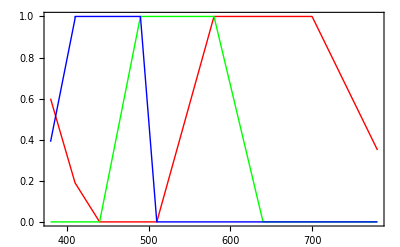

```mathematica
Plot[{toRGB[wavelength][[1]],toRGB[wavelength][[2]],toRGB[wavelength][[3]]},{wavelength,380,780},PlotStyle->{Red,Green,Blue},Frame->True]
```

```mathematica
Clear[wavelength]
```

```mathematica
toRGB[wavelength_]:=Piecewise[{{{0.6 - 0.41(wavelength-380)/30,0,0.39 + 0.6(wavelength-380)/30},wavelength ≥ 380.0 && wavelength ≤ 410.0},{{0.19 - 0.19(wavelength-410)/30,0,1},wavelength ≥ 410.0 && wavelength ≤ 440.0},{{0,1 - (490-wavelength)/50,1},wavelength ≥ 440.0 && wavelength ≤ 490.0},{{0,1,(510-wavelength)/20},wavelength ≥ 490.0 && wavelength ≤ 510.0},{{1 - (580-wavelength)/70,1,0},wavelength ≥ 510.0 && wavelength ≤ 580.0},
{{1,(640-wavelength)/60,0},wavelength ≥ 580.0 && wavelength ≤ 640.0},
{{1,0,0},wavelength ≥ 640.0 && wavelength ≤ 700.0},
{{0.35 + 0.65(780-wavelength)/80,0,0},wavelength ≥ 700.0 && wavelength ≤ 780.0}}]
```

```mathematica
toRGB[wavelength_]:=Piecewise[{{{0.6 - 0.41(410-wavelength)/30,0,0.39 + 0.6(410-wavelength)/30},wavelength ≥ 380.0 && wavelength ≤ 410.0},{{0.19 - 0.19(440-wavelength)/30,0,1},wavelength ≥ 410.0 && wavelength ≤ 440.0},{{0,1 - (490-wavelength)/50,1},wavelength ≥ 440.0 && wavelength ≤ 490.0},{{0,1,(510-wavelength)/20},wavelength ≥ 490.0 && wavelength ≤ 510.0},{{1 - (580-wavelength)/70,1,0},wavelength ≥ 510.0 && wavelength ≤ 580.0},
{{1,(640-wavelength)/60,0},wavelength ≥ 580.0 && wavelength ≤ 640.0},
{{1,0,0},wavelength ≥ 640.0 && wavelength ≤ 700.0},
{{0.35 + 0.65(780-wavelength)/80,0,0},wavelength ≥ 700.0 && wavelength ≤ 780.0}}]
```

```mathematica
toRGB[λ]
```

Piecewise[{{{0.6-0.0136667 (-380+λ),0,0.39+0.02 (-380+λ)}, λ≥380.&&λ≤410.}, {{0.19-0.00633333 (-410+λ),0,1}, λ≥410.&&λ≤440.}, {{0,1+1/50 (-490+λ),1}, λ≥440.&&λ≤490.}, {{0,1,(510-λ)/20}, λ≥490.&&λ≤510.}, {{1+1/70 (-580+λ),1,0}, λ≥510.&&λ≤580.}, {{1,(640-λ)/60,0}, λ≥580.&&λ≤640.}, {{1,0,0}, λ≥640.&&λ≤700.}, {{0.35+0.008125 (780-λ),0,0}, λ≥700.&&λ≤780.}, {0, True}}]

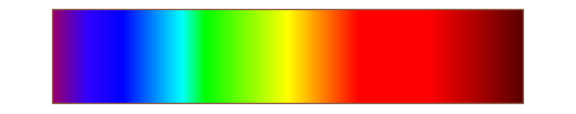

```mathematica
ParametricPlot[{x,y},{x,380,780},{y,0,1},
ColorFunction->(RGBColor@@toRGB[#1]&),
ColorFunctionScaling->False, (* Do *not* scale #1 to 0..1! *)
BaseStyle->{FontSize->14},
AxesOrigin->{400,0},
Axes->None,
Ticks->None,
Frame->False,
Mesh->None,ImagePadding->All,
AspectRatio->.2,
PlotPoints->{1024,2},
ImageSize->Large
]
```

```mathematica
OxyHemoglobin={415,540,570}
DeoxyHemoglobin={430,555}
```

{415,540,570}

{430,555}

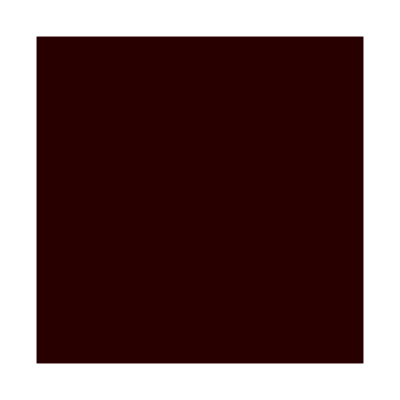

```mathematica
Graphics[{RGBColor[0.15833333333333333,0,0],Rectangle[{0,0},{1,1}]}]
```

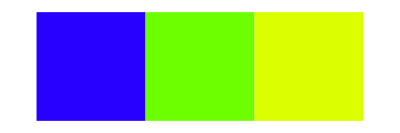

```mathematica
Graphics[{RGBColor[0.1583,0,1],Rectangle[{0,0},{1,1}],RGBColor[3/7,1,0],Rectangle[{1,0},{2,1}],RGBColor[6/7,1,0],Rectangle[{2,0},{3,1}]}]
```

```mathematica
Graphics[{RGBColor[Transpose[OxyHemoglobinRGB][[1]]],Rectangle[{0,0},{1,1}],RGBColor[Transpose[OxyHemoglobinRGB][[2]]],Rectangle[{1,0},{2,1}],RGBColor[Transpose[OxyHemoglobinRGB][[3]]],Rectangle[{2,0},{3,1}]}]
```

-Graphics-

```mathematica
OxyHemoglobinRGB = Transpose[Map[toRGB,OxyHemoglobin]]
DeoxyHemoglobinRGB = Transpose[Map[toRGB,DeoxyHemoglobin]]
```

{{0.158333,3/7,6/7},{0,1,1},{1,0,0}}

{{0.0633333,9/14},{0,1},{1,0}}

```mathematica
nYAB[-0.1537].OxyHemoglobinRGB + {{0,0,0},{0.5,0.5,0.5},{0.5,0.5,0.5}}
```

{{0.193056,0.238095,0.309524},{0.846045,0.0783929,0.156786},{0.161267,0.632185,0.846471}}

```mathematica
AppendTo[$Path, NotebookDirectory[]]
```

```mathematica
AbsOxyHemo = Import["AbsorbanceOxyHemo.csv"];
AbsDeOxyHemo = Import["AbsorbanceDeOxyHemo.csv"];
AbsMel= Import["AbsorbanceMel.csv"];
```

```mathematica
ScatOxyHemo = AbsOxyHemo;
ScatOxyHemo[[All,2]] = 1- AbsOxyHemo[[All,2]];
ScatDeOxyHemo = AbsDeOxyHemo;
ScatDeOxyHemo[[All,2]] = 1- AbsDeOxyHemo[[All,2]];
ScatMel = AbsMel;
ScatMel[[All,2]] = 1- AbsMel[[All,2]];
```

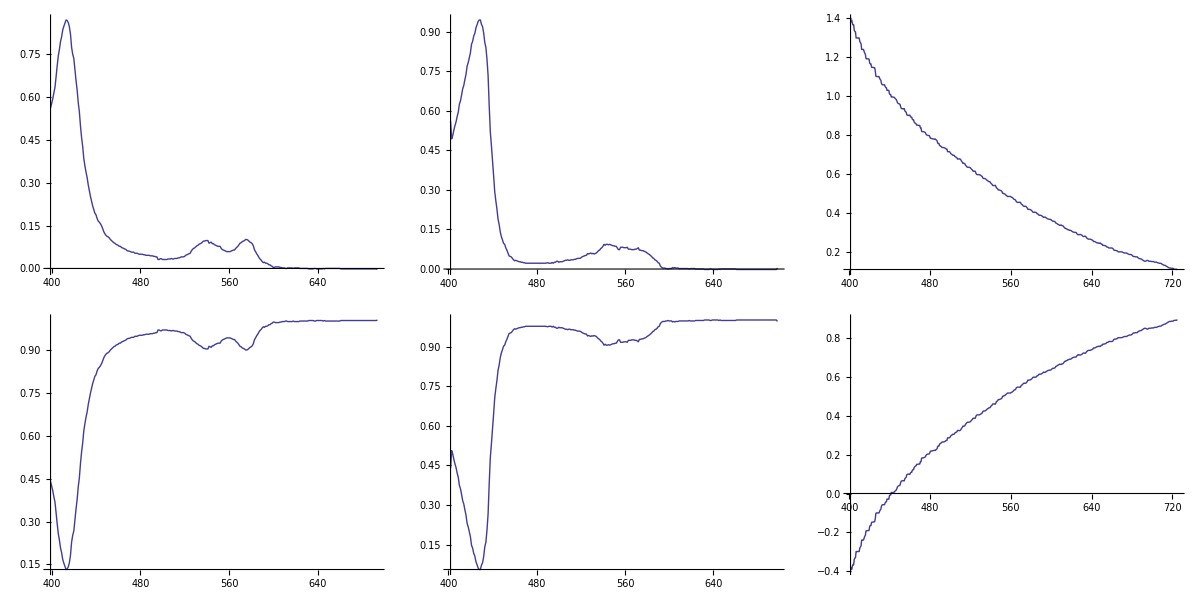

```mathematica
Grid[{{ListLinePlot[AbsOxyHemo,PlotRange->All],ListLinePlot[AbsDeOxyHemo,PlotRange->All],ListLinePlot[AbsMel,PlotRange->All]},
{ListLinePlot[ScatOxyHemo,PlotRange->All],ListLinePlot[ScatDeOxyHemo,PlotRange->All],ListLinePlot[ScatMel,PlotRange->All]}}]
```

```mathematica
AppendTo[$Path, NotebookDirectory[]]
```

{C:\Program Files\Wolfram Research\Mathematica\9.0\SystemFiles\Links,C:\Users\Jasper\AppData\Roaming\Mathematica\Kernel,C:\Users\Jasper\AppData\Roaming\Mathematica\Autoload,C:\Users\Jasper\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\Jasper,C:\Program Files\Wolfram Research\Mathematica\9.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\9.0\AddOns\LegacyPackages,C:\Program Files\Wolfram Research\Mathematica\9.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\9.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\9.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\9.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\9.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\9.0\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\9.0\SystemFiles\Data\ICC,D:/JaspersDocuments/Developer/ColorSpaceConversion/\,D:\JaspersDocuments\Developer\ColorSpaceConversion\,D:\JaspersDocuments\Developer\ColorSpaceConversion\Mathgematica\,D:\JaspersDocuments\Developer\ColorSpaceConversion\Mathgematica\,D:\JaspersDocuments\Developer\ColorSpaceConversion\Mathgematica\,D:\My Documents\Developer\ColorSpaceConversion\Mathgematica\,.\Developer\ColorSpaceConversion\Mathgematica\,D:\JaspersDocuments\Developer\ColorSpaceConversion\Mathematica\}

```mathematica
$Path
```

{C:\Program Files\Wolfram Research\Mathematica\9.0\SystemFiles\Links,C:\Users\Jasper\AppData\Roaming\Mathematica\Kernel,C:\Users\Jasper\AppData\Roaming\Mathematica\Autoload,C:\Users\Jasper\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\Jasper,C:\Program Files\Wolfram Research\Mathematica\9.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\9.0\AddOns\LegacyPackages,C:\Program Files\Wolfram Research\Mathematica\9.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\9.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\9.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\9.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\9.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\9.0\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\9.0\SystemFiles\Data\ICC}

```mathematica
$PWD
```

$PWD

```mathematica
NotebookDirectory[]
```

D:\JaspersDocuments\Developer\ColorSpaceConversion\Mathematica\

```mathematica
Directory[]
```

D:\JaspersDocuments

```mathematica
FindFile["AbsorbanceOxyHemo.csv"]
```

$Failed

```mathematica
$HomeDirectory
```

C:\Users\Jasper